```mathematica
(*Define Directions*)
xhat = {1,0};
yhat = {0,1};
thetahat = {1,0};
rhat = {0,1};

(*some nice helper functions*)
polarToCartesian[Θ_,R_]={R Cos[Θ],R Sin[Θ]};
rotToGrav[omega_,r_] = r*(omega^2);
cartesianToPolar[x_,y_] = {ArcTan[x,y],Sqrt[x^2 + y^2]};

(*Define functions for different projectile motions*)
(*arclength equation*)
arcLengthProjectileMotion[t_,v0_,ΘThrow_,Θinit_,r0_,omega_,R_] = Module[{
(*Define Local variables*)
refPointOnShip, startPointOnShip,projectilePath,initProjectileVelocity
},
refPointOnShip =  R{Cos[omega*t+Θinit],Sin[omega *t +Θinit]};
startPointOnShip =  r0{Cos[Θinit],Sin[Θinit]};
initProjectileVelocity = {v0 Cos[ΘThrow + Pi/2 +Θinit ],v0 Sin[ΘThrow + Pi/2 + Θinit]} +  r0*omega*{-Sin[Θinit],Cos[Θinit ]};
projectilePath = initProjectileVelocity * t +startPointOnShip;
{R*(ArcTan[xhat.projectilePath,yhat.projectilePath]),R-Sqrt[projectilePath.projectilePath]}];
gravProjectileMotion [t_,v0_,Θ_,x0_,y0_,g_] = {
(*horizontal component*)
v0 t Cos[Θ]+x0,
(*vertical Component*)
-g/2*t^2 + v0 t Sin[Θ] + y0
};
```

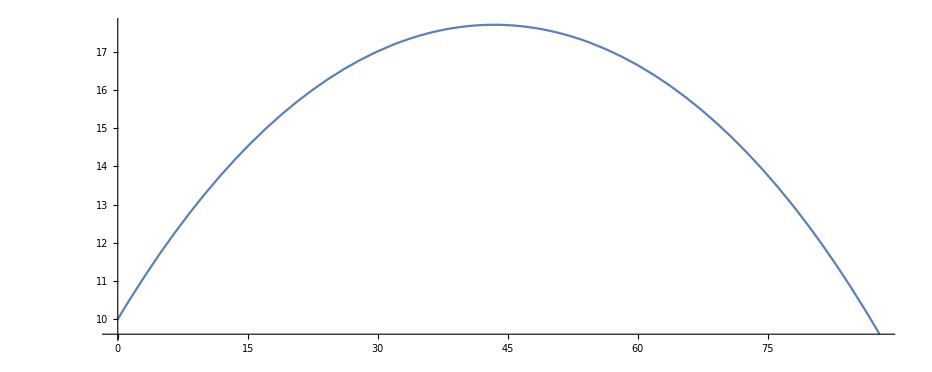

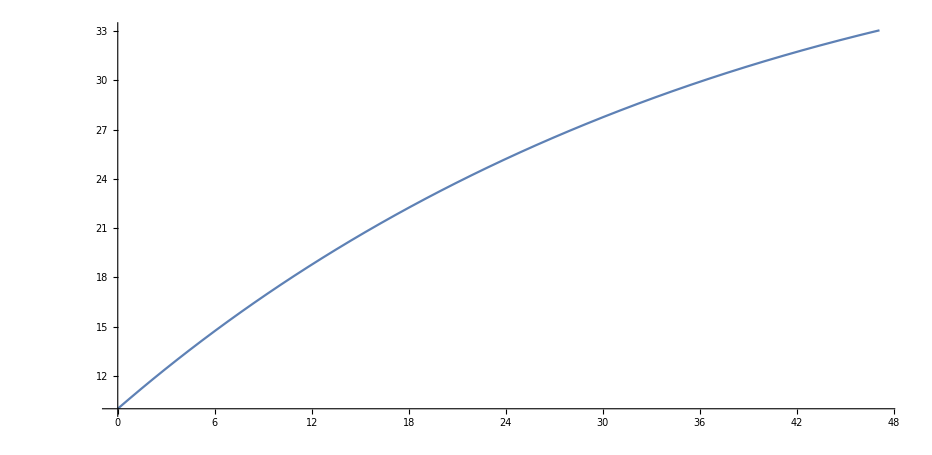

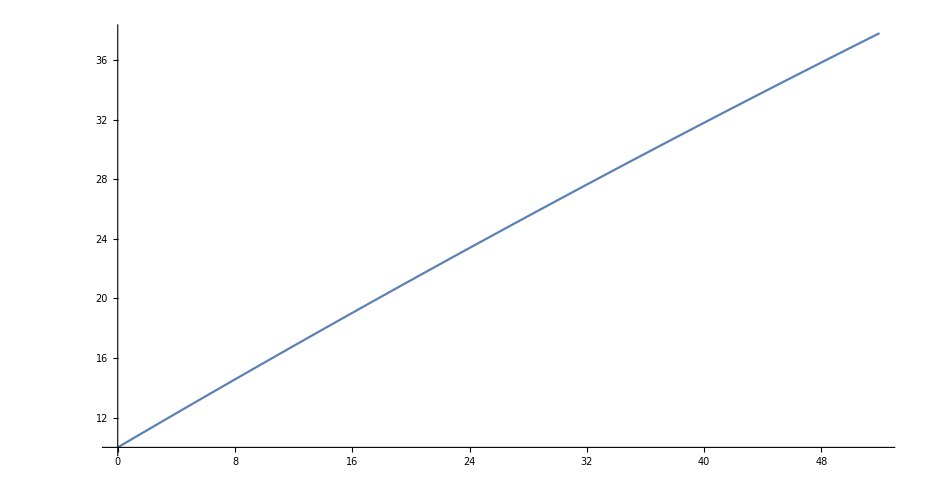

```mathematica
ArcLengthPlotRight = ParametricPlot[arcLengthProjectileMotion[t,3,Pi/6,0,100,.01,110],{t,0,20}]
ArcLengthPlotLeft = ParametricPlot[{-arcLengthProjectileMotion[t,3,5Pi/6,0,100,.01,110].xhat,arcLengthProjectileMotion[t,3,5Pi/6,0,100,.01,110].yhat},{t,0,20}]
equivGrav = rotToGrav[.01,110];
gravProjectileMotionPlot = ParametricPlot[gravProjectileMotion[t,3,Pi/6,0,10,equivGrav],{t,0,20}]
```

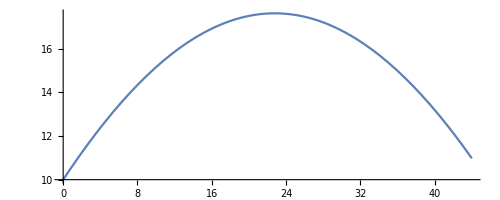

```mathematica
Show[genArcLengthPlot,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

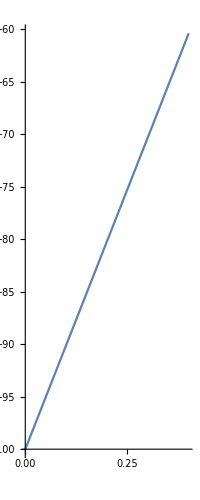

```mathematica
inertialPlot = ParametricPlot[Module[{arclen ,theta,radius},
arclen = arcLengthProjectileMotion[t,1.4,3Pi/4,-Pi/2,100,.01,110];
theta =( arclen.thetahat)/110 ;
radius = -1*arclen.rhat + 110;
{radius Cos[theta],radius Sin[theta]
}],{t,0,40}]
```

```mathematica
arcLengthProjectileMotion[t,2,Pi/4,0,r,.01,R].rhat*-1 + 110
```

110-R+√((√2+0.01 r)^2 t^2+(-r+1.41421 t)^2)